# Análisis de estados promedio bi y tripartitos (último capítulo)

Aquí se harán los cálculos del último capítulo. Para varios estados promedio (generados con el algoritmo MH) se les calculará la pureza, coherencias y entrelazamiento

```mathematica
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
<<"Quantum`"
<<"MaTeX`"
```

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[b:{__?MatrixQ}] is Protected.

SetDelayed::write: Tag PermutationMatrix in PermutationMatrix[p_List] is Protected.

```mathematica
rzs = {0, 0.5, 0.8};
(*parámetros bipartitos*)
swapPs = {0.3, 0.5, 0.8};
```

```mathematica
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs;
```

## Importando muestras

### Caso de 2 qubits

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/final_samples

```mathematica
mhSampleR0Pp3 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0_p=0.3.wl"][[1]];
mhSampleR0Pp5 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0_p=0.5.wl"][[1]];
mhSampleR0Pp8 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0_p=0.8.wl"][[1]];
```

```mathematica
Clear[mhSampleR0Pp3, mhSampleR0Pp5, mhSampleR0Pp8]
```

```mathematica
mhSampleRp5Pp3 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0.5_p=0.3.wl"][[1]];
mhSampleRp5Pp5 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0.5_p=0.5.wl"][[1]];
mhSampleRp5Pp8 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0.5_p=0.8.wl"][[1]];
```

```mathematica
Clear[mhSampleRp5Pp3, mhSampleRp5Pp5, mhSampleRp5Pp8]
```

```mathematica
mhSampleRp8Pp3 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0.8_p=0.3.wl"][[1]];
mhSampleRp8Pp5 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0.8_p=0.5.wl"][[1]];
mhSampleRp8Pp8 = Get["MHsample_N=200000_delta=0.05_beta=100_rz=0.8_p=0.8.wl"][[1]];
```

```mathematica
Clear[mhSampleRp8Pp3, mhSampleRp8Pp5, mhSampleRp8Pp8]
```

## Estados promedio

### Caso 2 qubits

```mathematica
avgR0Pp3MH = preimageMean[mhSampleR0Pp3[[2,1]]];
avgR0Pp5MH = preimageMean[mhSampleR0Pp5[[2,1]]];
avgR0Pp8MH = preimageMean[mhSampleR0Pp8[[2,1]]];
```

```mathematica
avgRp5Pp3MH = preimageMean[mhSampleRp5Pp3[[2,1]]];
avgRp5Pp5MH = preimageMean[mhSampleRp5Pp5[[2,1]]];
avgRp5Pp8MH = preimageMean[mhSampleRp5Pp8[[2,1]]];
```

```mathematica
avgRp8Pp3MH = preimageMean[mhSampleRp8Pp3[[2,1]]];
avgRp8Pp5MH = preimageMean[mhSampleRp8Pp5[[2,1]]];
avgRp8Pp8MH = preimageMean[mhSampleRp8Pp8[[2,1]]];
```

```mathematica
(*brutales*)
avgR0Pp3BRUTAL = preimageMean[sampleR0Pp3BRUTAL];
avgR0Pp5BRUTAL = preimageMean[sampleR0Pp5BRUTAL];
avgR0Pp8BRUTAL = preimageMean[sampleR0Pp8BRUTAL];
avgRp5Pp3BRUTAL = preimageMean[sampleRp5Pp3BRUTAL];
avgRp5Pp5BRUTAL = preimageMean[sampleRp5Pp5BRUTAL];
avgRp5Pp8BRUTAL = preimageMean[sampleRp5Pp8BRUTAL];
avgRp8Pp3BRUTAL = preimageMean[sampleRp8Pp3BRUTAL];
avgRp8Pp5BRUTAL = preimageMean[sampleRp8Pp5BRUTAL];
avgRp8Pp8BRUTAL = preimageMean[sampleRp8Pp8BRUTAL];
```

## Pureza

```mathematica
(*rz = 0 y todas las swapPs*)
Chop[Purity[#]]& /@ {avgR0Pp3MH, avgR0Pp5MH, avgR0Pp8MH}
```

{0.263647,0.325467,0.265059}

```mathematica
(*rz = 0.5 y todas las swapPs*)
Chop[Purity[#]]& /@ {avgRp5Pp3MH, avgRp5Pp5MH, avgRp5Pp8MH}
```

{0.396185,0.468811,0.366304}

```mathematica
(*rz = 0.8 y todas las swapPs*)
Chop[Purity[#]]& /@ {avgRp8Pp3MH, avgRp8Pp5MH, avgRp8Pp8MH}
```

{0.671414,0.728692,0.568572}

## Coherencias

```mathematica
SetAttributes[coherencesVector, HoldFirst];
coherencesVector[rho_]:= Join @@ Array[rho[[#, # + 1 ;;]]&, Length[rho] - 1];
coherenceMeasure[rho_]:= Norm[coherencesVector[rho]];
```

```mathematica
(*rz = 0 y todas las swapPs*)
coherenceMeasure[#]& /@ {avgR0Pp3MH, avgR0Pp5MH, avgR0Pp8MH}
```

{0.0545502,0.163818,0.0684487}

```mathematica
(*rz = 0.5 y todas las swapPs*)
coherenceMeasure[#]& /@ {avgRp5Pp3MH, avgRp5Pp5MH, avgRp5Pp8MH}
```

{0.106556,0.127192,0.0593869}

```mathematica
(*rz = 0.8 y todas las swapPs*)
coherenceMeasure[#]& /@ {avgRp8Pp3MH, avgRp8Pp5MH, avgRp8Pp8MH}
```

{0.0471918,0.0595731,0.0618431}

## Entrelazamiento

### Caso de 2 qubits

```mathematica
(*Concurrencia y entanglement of formation*)
h[x_]:= -x Log[2, x] - (1-x) Log[2, 1-x];
h[1]:= 0;
entanglementOfFormation[rho_]:= h[(1+Sqrt[1-Concurrence[rho]^2])/2]
```

```mathematica
(*rz = 0 y todas las swapPs*)
entanglementOfFormation[#]& /@ {avgR0Pp3MH, avgR0Pp5MH, avgR0Pp8MH}
```

{0,0,0}

```mathematica
(*rz = 0.5 y otdas las swapPs*)
entanglementOfFormation[#]& /@ {avgRp5Pp3MH, avgRp5Pp5MH, avgRp5Pp8MH}
```

{0,0,0}

```mathematica
(*rz = 0.8 y todas las swapPs*)
entanglementOfFormation[#]& /@ {avgRp8Pp3MH, avgRp8Pp5MH, avgRp8Pp8MH}
```

{0,0,0}

### Caso de 3 qubits...

## Gráficas cilíndricas

```mathematica
generalLegend = 
Grid[{{SwatchLegend[{Darker[Red,.2], Darker[Green, .2]}, 
					MaTeX[{"\\tr_A", "\\tr_B"}, Preamble->{"\\usepackage{physics, newtxmath}"}, FontSize->20], 
					LegendLabel->MaTeX["\\text{Metropolis-Hastings}", FontSize->20], 
					LegendLayout->"Row",
					LegendMarkerSize->20]},
	   {SwatchLegend[{Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, 
	                 MaTeX[{"\\tr_A", "\\tr_B"}, Preamble->{"\\usepackage{physics, newtxmath}"}, FontSize->20], 
	                 LegendLabel->MaTeX["\\text{Brutal}", FontSize->20], 
	                 LegendLayout->"Row",
	                 LegendMarkerSize->20]}
}];
```

### Objetivo r_z = 0

#### p = 0.3

```mathematica
sampleR0Pp3BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.m"]];
```

```mathematica
cylPlotsR0Pp3BRUTAL = tripleCylindricalPlotNoFilling[sampleR0Pp3BRUTAL, 0, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
cylPlotsR0Pp3MH = tripleCylindricalPlotNoFilling[mhSampleR0Pp3[[2,1]], 0, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.2}, {0,6.2}, {-0.2,0.2}}, {200, Automatic, 200}];
```

```mathematica
spherePlotR0Pp3MH = visualizeBipartiteSystem[mhSampleR0Pp3[[2,1, 100000;;]]];
spherePlotR0Pp3BRUTAL = visualizeBipartiteSystem[sampleR0Pp3BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0,\\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsR0Pp3MH[[i]], cylPlotsR0Pp3BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotR0Pp3MH, spherePlotR0Pp3BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_R0Pp3.pdf", %106]
```

mhFinalResults_R0Pp3.pdf

#### p = 0.5

```mathematica
sampleR0Pp5BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.m"]];
```

```mathematica
cylPlotsR0Pp5BRUTAL = tripleCylindricalPlotNoFilling[sampleR0Pp5BRUTAL, 0, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
cylPlotsR0Pp5MH = tripleCylindricalPlotNoFilling[mhSampleR0Pp5[[2,1]], 0, {Darker[Red,.2], Darker[Green, .2]}, {Full, {0,6.2}, Full}];
```

```mathematica
spherePlotR0Pp5MH = visualizeBipartiteSystem[mhSampleR0Pp5[[2,1,100000;;]]];
spherePlotR0Pp5BRUTAL = visualizeBipartiteSystem[sampleR0Pp5BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0,\\, p = 0.5", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsR0Pp5MH[[i]], cylPlotsR0Pp5BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotR0Pp5MH, spherePlotR0Pp5BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_R0Pp5.pdf", %111]
```

mhFinalResults_R0Pp5.pdf

#### p = 0.8

```mathematica
sampleR0Pp8BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.m"]];
```

```mathematica
cylPlotsR0Pp8BRUTAL = tripleCylindricalPlotNoFilling[sampleR0Pp8BRUTAL, 0, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
cylPlotsR0Pp8MH = tripleCylindricalPlotNoFilling[mhSampleR0Pp8[[2,1]], 0, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.2}, {0,6.2}, {-0.15,0.15}}, {200, Automatic, 200}];
```

```mathematica
spherePlotR0Pp8MH = visualizeBipartiteSystem[mhSampleR0Pp8[[2,1,100000;;]]];
spherePlotR0Pp8BRUTAL = visualizeBipartiteSystem[sampleR0Pp8BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0,\\, p = 0.8", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsR0Pp8MH[[i]], cylPlotsR0Pp8BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotR0Pp8MH, spherePlotR0Pp8BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_R0Pp8.pdf", %116]
```

mhFinalResults_R0Pp8.pdf

### Objetivo r_z = 0.5

#### p = 0.3

```mathematica
sampleRp5Pp3BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"]];
```

```mathematica
cylPlotsRp5Pp3BRUTAL = tripleCylindricalPlotNoFilling[sampleRp5Pp3BRUTAL, 0.5, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {{0,0.9}, {0,6.21}, Full}];
cylPlotsRp5Pp3MH = tripleCylindricalPlotNoFilling[mhSampleRp5Pp3[[2,1]], 0.5, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.9}, {0,6.2}, Full}, {Automatic, Automatic, 30}];
```

```mathematica
spherePlotRp5Pp3MH = visualizeBipartiteSystem[mhSampleRp5Pp3[[2,1,100000;;]]];
spherePlotRp5Pp3BRUTAL = visualizeBipartiteSystem[sampleRp5Pp3BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.5,\\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp5Pp3MH[[i]], cylPlotsRp5Pp3BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp5Pp3MH, spherePlotRp5Pp3BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp5Pp3.pdf", %101]
```

mhFinalResults_Rp5Pp3.pdf

#### p = 0.5

```mathematica
sampleRp5Pp5BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.5.m"]];
```

```mathematica
cylPlotsRp5Pp5BRUTAL = tripleCylindricalPlotNoFilling[sampleRp5Pp5BRUTAL, 0.5, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {{0,0.85}, {0,6.2}, Full}];
cylPlotsRp5Pp5MH = tripleCylindricalPlotNoFilling[mhSampleRp5Pp5[[2,1]], 0.5, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.85}, {0,6.2}, {-0.15, 0.15}}, {Automatic, Automatic, 100}];
```

```mathematica
spherePlotRp5Pp5MH = visualizeBipartiteSystem[mhSampleRp5Pp5[[2,1,100000;;]]];
spherePlotRp5Pp5BRUTAL = visualizeBipartiteSystem[sampleRp5Pp5BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.5,\\, p = 0.5", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp5Pp5MH[[i]], cylPlotsRp5Pp5BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp5Pp5MH, spherePlotRp5Pp5BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp5Pp5.pdf", %137]
```

mhFinalResults_Rp5Pp5.pdf

#### p = 0.8

```mathematica
sampleRp5Pp8BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.5.m"]];
```

```mathematica
cylPlotsRp5Pp8BRUTAL = tripleCylindricalPlotNoFilling[sampleRp5Pp8BRUTAL, 0.5, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}];
cylPlotsRp5Pp8MH = tripleCylindricalPlotNoFilling[mhSampleRp5Pp8[[2,1]], 0.5, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.7}, {0,6.2}, Full}, {Automatic, Automatic, 30}];
```

```mathematica
spherePlotRp5Pp8MH = visualizeBipartiteSystem[mhSampleRp5Pp8[[2,1,100000;;]]];
spherePlotRp5Pp8BRUTAL = visualizeBipartiteSystem[sampleRp5Pp8BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.5,\\, p = 0.8", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp5Pp8MH[[i]], cylPlotsRp5Pp8BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp5Pp8MH, spherePlotRp5Pp8BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp5Pp8.pdf", %151]
```

mhFinalResults_Rp5Pp8.pdf

### Objetivo r_z = 0.8

#### p = 0.3

```mathematica
sampleRp8Pp3BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.8.m"]];
```

```mathematica
cylPlotsRp8Pp3BRUTAL = tripleCylindricalPlotNoFilling[sampleRp8Pp3BRUTAL, 0.8, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}];
cylPlotsRp8Pp3MH = tripleCylindricalPlotNoFilling[mhSampleRp8Pp3[[2,1]], 0.8, {Darker[Red,.2], Darker[Green, .2]}, {Full, {0,6.2}, Full}, {Automatic, Automatic, 50}];
```

```mathematica
spherePlotRp8Pp3MH = visualizeBipartiteSystem[mhSampleRp8Pp3[[2,1,100000;;]]];
spherePlotRp8Pp3BRUTAL = visualizeBipartiteSystem[sampleRp8Pp3BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.8,\\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp8Pp3MH[[i]], cylPlotsRp8Pp3BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp8Pp3MH, spherePlotRp8Pp3BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp8Pp3.pdf", %172]
```

mhFinalResults_Rp8Pp3.pdf

#### p = 0.5

```mathematica
sampleRp8Pp5BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.8.m"]];
```

```mathematica
cylPlotsRp8Pp5BRUTAL = tripleCylindricalPlotNoFilling[sampleRp8Pp5BRUTAL, 0.8, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}];
cylPlotsRp8Pp5MH = tripleCylindricalPlotNoFilling[mhSampleRp8Pp5[[2,1]], 0.8, {Darker[Red,.2], Darker[Green, .2]}, {{0,0.7}, {0,6.2}, {-0.1,0.1}}, {30, Automatic, 200}];
```

```mathematica
spherePlotRp8Pp5MH = visualizeBipartiteSystem[mhSampleRp8Pp5[[2,1,100000;;]]];
spherePlotRp8Pp5BRUTAL = visualizeBipartiteSystem[sampleRp8Pp5BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.8,\\, p = 0.5", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp8Pp5MH[[i]], cylPlotsRp8Pp5BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp8Pp5MH, spherePlotRp8Pp5BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp8Pp5.pdf", %192]
```

mhFinalResults_Rp8Pp5.pdf

#### p = 0.8

```mathematica
sampleRp8Pp8BRUTAL = 
ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.8.m"]];
```

```mathematica
cylPlotsRp8Pp8BRUTAL = tripleCylindricalPlotNoFilling[sampleRp8Pp8BRUTAL, 0.8, {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}, {Full, {0,6.2}, Full}];
cylPlotsRp8Pp8MH = tripleCylindricalPlotNoFilling[mhSampleRp8Pp8[[2,1]], 0.8, {Darker[Red,.2], Darker[Green, .2]}, {Full, {0,6.2}, {-1, 0.2}}, {Automatic, Automatic, 30}];
```

```mathematica
spherePlotRp8Pp8MH = visualizeBipartiteSystem[mhSampleRp8Pp8[[2,1,100000;;]]];
spherePlotRp8Pp8BRUTAL = visualizeBipartiteSystem[sampleRp8Pp8BRUTAL[[1;;2000]], {Hue[0.11,0.9,0.85], Hue[0.55,1,0.7]}];
```

```mathematica
Grid[{{MaTeX["r_z = 0.8,\\, p = 0.8", Preamble->{"\\usepackage{newtxmath}"}, FontSize->20], SpanFromLeft, SpanFromLeft},
			  Table[Show[cylPlotsRp8Pp8MH[[i]], cylPlotsRp8Pp8BRUTAL[[i]], ImageSize->250], {i,3}],
			  (Show[#, ImageSize->250]& /@ {spherePlotRp8Pp8MH, spherePlotRp8Pp8BRUTAL})~Join~{generalLegend}
}]
```

```mathematica
Export["mhFinalResults_Rp8Pp8.pdf", %209]
```

mhFinalResults_Rp8Pp8.pdf

## Fidelidades

```mathematica
MapThread[fidelity[#1, #2]&, {{avgR0Pp3BRUTAL, avgR0Pp5BRUTAL, avgR0Pp8BRUTAL}, 
							  {avgR0Pp3MH, avgR0Pp5MH, avgR0Pp8MH}}]
```

{0.989085,0.99577,0.989547}

```mathematica
MapThread[fidelity[#1, #2]&, {{avgRp5Pp3BRUTAL, avgRp5Pp5BRUTAL, avgRp5Pp8BRUTAL}, 
							  {avgRp5Pp3MH, avgRp5Pp5MH, avgRp5Pp8MH}}]
```

{0.996105,0.997102,0.996952}

```mathematica
MapThread[fidelity[#1, #2]&, {{avgRp8Pp3BRUTAL, avgRp8Pp5BRUTAL, avgRp8Pp8BRUTAL},
							  {avgRp8Pp3MH, avgRp8Pp5MH, avgRp8Pp8MH}}]
```

{0.99971,0.998514,0.997474}

## Tiempos de ejecución

```mathematica
betas = {100, 250, 400, 600, 750, 1000};
deltas = {0.005, 0.01, 0.03, 0.05, 0.07, 0.1};
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/distintas_Nbetasydeltas_Rp5Pp3_DOS/exectimes"]
```

/media/storage/ciencia/investigacion/tesis/mh_muestras_GOOD/distintas_Nbetasydeltas_Rp5Pp3_DOS/exectimes

```mathematica
timesN9 = Outer[Get["execTimes_beta="<>ToString[#2]<>"_delta="<>ToString[#1]<>"_rz=0.5_p=0.3_allN.wl"][[10]]&, deltas, betas];
```

```mathematica
timeData = Map[MapThread[{#1, #2}&, {betas, #}]&, timesN9];
```

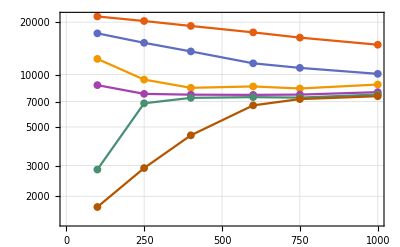

```mathematica
(*Tiempos de ejecución MH VS beta y diferentes deltas. Todo para N = un millón*)
ListLogPlot[timeData, PlotTheme->"Scientific", 
FrameLabel->MaTeX[{"\\text{Estrechez}\\,\\,(\\beta)", "\\text{Tiempo de ejecución}\\,\\,[s]"}, Preamble->{"\\usepackage{newtxmath}"}], 
PlotLegends->LineLegend[MaTeX[deltas], LegendLabel->MaTeX["\\delta", Preamble->{"\\usepackage{newtxmath}"}]],
Joined->True, Mesh->All, MeshStyle->PointSize[0.014], GridLines->Automatic, FrameStyle->Black]
```